Program calculating rate constants for van der Waals interaction for arbitrary boundary conditions at short range 
Everything in units of R_vdw and E_vdw (characteristic length and energy for van der Waals interaction)

```mathematica
SetDirectory[NotebookDirectory[]]
```

Parameters:
Lmax - maximal value of angular momentum L
xi - minimal value of r in the grid
nptl - number of points to tabulate the wavelenght
npt - numeber of point per de Broglie wavelenght in the grid 
energ - energy of particles
epsi - small number used to determine initial point of integration
epsf - small number used to determine final point of integration
dxf - step used to determine the final point of integration

Table of parametrs

```mathematica
Lmin=0;Lmax=20;nptl=500;npt=30;epsf=10^-12;epsi=10^-4;dxf=10;
```

```mathematica
KtoEh=3.1668153 10^(-6);
HztoEh=1.519829 10^(-16);
massunit=1.661 10^(-24)/(9.110 10^(-28));
μ=81.25 massunit; 
Debye=0.393456;
d=9/(137*2);
m = 9.18 BohrM;
```

```mathematica
C6=2277;
```

```mathematica
R6=(2 μ C6)^(1/4);E6=1/(2 μ R6^2);
```

```mathematica
abar=(Pi/8)/Gamma[5/4]^2;abar1=Gamma[1/4]^6/(144 Pi^2 Gamma[3/4]^2)abar ;
C3=2d^2;R3=2 μ C3/R6;E3=(1/(2μ (R6 R3)^2))/E6;
β=R3
```

3.9669

```mathematica
xf=200;
```

```mathematica
freq=30000; 
freqz=0.1 freq;
ω=2 π freq HztoEh; ωz=2 π freqz HztoEh;aHO=(1/Sqrt[μ ω])/R6; aHOz=(1/Sqrt[μ ωz])/R6;
α=(1/aHO)^4;
αz=(1/aHOz)^4;
Ω=2 Sqrt[α];
Ωz=2 Sqrt[αz];
```

Potentials

```mathematica
Vho[l1_,ml1_,l2_,ml2_]:= (If[l1==l2,1,0]If[ml1==ml2,1,0]-(1-αz/α)If[ml1==ml2,1,0]/3((-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1] 2 ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}] + If[l1==l2,1,0]));
Vedd[l1_,ml1_,l2_,ml2_]:=-(-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1]  ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}];(*Dodać symbol wignera*)
Vmdd[l1_,ml1_,l2_,ml2_]:=-(-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1]  ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}];
Vvdw[l1_,ml1_,l2_,ml2_]:= -If[l1==l2,1,0]If[ml1==ml2,1,0];
```

```mathematica
Veddtab=Developer`ToPackedArray[N[Table[Vedd[l1,0,l2,0],{l1,0,Lmax},{l2,0,Lmax}]]];
Vmddtab=Developer`ToPackedArray[N[Table[Vmdd[l1,0,l2,0],{l1,0,Lmax},{l2,0,Lmax}]]];
Vvdwtab=Developer`ToPackedArray[N[Table[Vvdw[l1,0,l2,0],{l1,0,Lmax},{l2,0,Lmax}]]];
Vhotab=Developer`ToPackedArray[N[Table[Vho[l1,0,l2,0],{l1,0,Lmax},{l2,0,Lmax}]]];
Vcftab = Developer`ToPackedArray[N[Table[If[l1==l2,l1(l1+1),0],{l1,0,Lmax},{l2,0,Lmax}]]];
Veddtab2=Developer`ToPackedArray[N[Table[Vedd[l1,0,l2,0],{l1,1,Lmax},{l2,1,Lmax}]]];
Vmddtab2=Developer`ToPackedArray[N[Table[Vmdd[l1,0,l2,0],{l1,1,Lmax},{l2,1,Lmax}]]];
Vvdwtab2=Developer`ToPackedArray[N[Table[Vvdw[l1,0,l2,0],{l1,1,Lmax},{l2,1,Lmax}]]];
Vhotab2=Developer`ToPackedArray[N[Table[Vho[l1,0,l2,0],{l1,1,Lmax},{l2,1,Lmax}]]];
Vcftab2 = Developer`ToPackedArray[N[Table[If[l1==l2,l1(l1+1),0],{l1,1,Lmax},{l2,1,Lmax}]]];
```

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{1,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{1,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{1,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{4,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{4,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{4,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

```mathematica
Vhotable[x_]:=N[(Table[Vhotab[[l1/2+1,l2/2+1]],{l1,0,Lmax},{l2,0,Lmax}])/.{r->x}];
```

Table of channels

```mathematica
TabCh={};Do[AppendTo[TabCh,{l(*,m*)}],{l,Lmin,Lmax}(*,{m,-l,l}*)];Nch=Length[TabCh];Id=IdentityMatrix[Lmax+1];Nch
```

21

Spherical Bessel functions

```mathematica
jl[l_,x_]:=Sqrt[Pi/(2x)]BesselJ[l+1/2,x];nl[l_,x_]:=(-1)^(l+1) Sqrt[Pi/(2x)]BesselJ[-l-1/2,x]
```

Matrix containg potential

```mathematica
V[r_]:=1/r^2 Vcftab + 1/r^6 Vvdwtab +β/r^3 Veddtab;
```

```mathematica
Length[V[1][[1]]]
```

21

Adiabatic potentials (diagonalized V[r]) + van der Waals potential

Take::take: Cannot take positions 1 through 10 in Eigenvalues[V2[0.500061]].

Take::take: Cannot take positions 1 through 10 in Eigenvalues[V2[0.565101]].

Take::take: Cannot take positions 1 through 10 in Eigenvalues[V2[0.638601]].

General::stop: Further output of Take::take will be suppressed during this calculation.

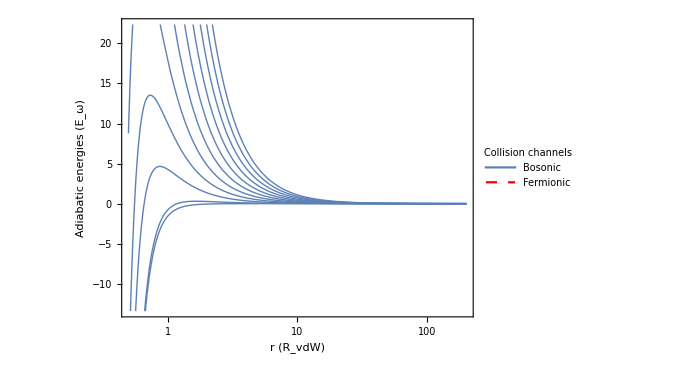

```mathematica
LogLinearPlot[{(Take[Sort[Eigenvalues[V[x]]],Lmax/2+1]),(Take[Sort[Eigenvalues[V2[x]]],Lmax/2])},{x,0.5,xf},
PlotRange->Automatic,AxesOrigin->{0.5,0},
AspectRatio->0.75,
Frame->True, FrameStyle->{{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]},{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]}},
PlotStyle->{Thick,{Red,Dashed}},PlotLegends->Placed[LineLegend[{Style["Bosonic",FontFamily->"Times",FontWeight->Bold],Style["Fermionic",FontFamily->"Times",FontWeight->Bold]}, LegendLabel->Style["Collision channels",FontSize->14, FontFamily->"Times",FontWeight->Bold],LegendFunction->(Framed[#,RoundingRadius->0,Background->White]&),LegendMargins->5],{Left,Top}],FrameLabel->{Style["r (R_vdW)",FontSize->20, FontFamily->"Times New Roman",FontWeight->Bold],Style["Adiabatic energies (E_ω)",FontSize->20,FontWeight->Bold, FontFamily->"Times"]},GridLines->Automatic, GridLinesStyle->Directive[Thin, Dashed, LightGray],ImagePadding->50,ImageSize->500]
```

```mathematica
N[abar]*4
```

1.91196

Short range solution for van der Waals potential, with the short range phase "phi"

```mathematica
sol0[r_,A_,B_]=A Sqrt[r]BesselJ[1/4,1/(2 r^2)]+B Sqrt[r] BesselY[1/4,1/(2 r^2)];
```

```mathematica
ash[phi_]:=abar (1+Tan[phi])
```

```mathematica
as[y_,s_]:=abar(s+y(1+(1-s)^2)/(ⅈ+y(1-s)));
ap[y_,s_,k_]:=-2 abar1  (k abar)^2  (y+ⅈ(s-1))/(y s+ⅈ(s-2))
```

Table of short range solutions

```mathematica
Psi0[r_,A_,B_]:=Table[If[n1==n2,sol0[r,A,B],0] ,{n1,1,Nch},{n2,1,Nch}]
```

Subroutine performing outward integration using renormalized Numerov method
It takes Psi0 as an initial condition

Parameters:
en - energy
n0 -  starting point (element of xt)
nf -  final point (element of xt)
phi - short-range phase

```mathematica
evolNumOut[en_?NumericQ,n0_?IntegerQ,nf_?IntegerQ,A_?NumericQ,B_?NumericQ,cl_?IntegerQ]:=
Module[{W,Qt,n,Rinv,h,h0,Ro,Rprod},

nodes=0;

Rout[n0]=Psi0[xt[[n0+1]],A,B].Inverse[Psi0[xt[[n0]],A,B]];
h=xt[[n0+1]]-xt[[n0]];
n=n0+1;

While[n<=nf,
h0=h;
h=xt[[n+1]]-xt[[n]];
Which[

Abs[h]>1.5 Abs[h0],
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].(2 Id -(5h^2/6)QT[[n]]-(Id+(h^2/12)QT[[n-2]]).Inverse[Rout[n-1].Rout[n-2]]);,

Abs[h]<0.75 Abs[h0],
Qt=en Id-V[(xt[[n]]+xt[[n-1]])/2];
Rinv=Inverse[2 Id-(h0^2/12)Qt].((Id+(h0^2/12)QT[[n-1]]).Inverse[Rout[n-1]]+Id+(h0^2/12)QT[[n]]);
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)Qt).Rinv);,

True,
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)QT[[n-1]]).Inverse[Rout[n-1]]);
];
n++;
];
Ro=Rout[nf];
Rprod=Inverse[Rout[n0]];Do[Rprod=Rprod.Inverse[Rout[n]],{n,n0+1,nf-1}];
Clear[W,n,Rinv,h,h0,Qt];
If[cl==1,Clear[Rout]];
{Ro,Rprod}]
```

Subroutine calculating K matrix

Parameters:
en -  the energy
A,B - constants determining boundary conditions at short range 

Output:
K matrix

```mathematica
KMatrix[en_?NumericQ,A_?NumericQ,B_?NumericQ]:=
Module[{J1,J2,N1,N2,Rn,K,r1,r2,kv,n1,n2,Rprod,R},
R=evolNumOut[en,1,nstep-1,A,B,1];
Rn=R[[1]];
kv=Sqrt[en];
r1=xt[[nstep-1]];
r2=xt[[nstep]];
J1=Table[If[n1==n2, kv r1 jl[TabCh[[n1,1]],kv r1],0],{n1,1,Nch},{n2,1,Nch}];
J2=Table[If[n1==n2,kv r2 jl[TabCh[[n1,1]],kv r2],0],{n1,1,Nch},{n2,1,Nch}];
N1=Table[If[n1==n2,kv r1 nl[TabCh[[n1,1]],kv r1],0],{n1,1,Nch},{n2,1,Nch}];
N2=Table[If[n1==n2,kv r2 nl[TabCh[[n1,1]],kv r2],0],{n1,1,Nch},{n2,1,Nch}];
K=-Inverse[Rn.N1-N2].(J2-Rn.J1);
K];
```

Subroutine calculating K and T matrices

Parameters:
en -  the energy
A,B - constants determining boundary conditions at short range 

Output:
K matrix
T matrix

```mathematica
KCTMatrix[en_?NumericQ,A_?NumericQ,B_?NumericQ]:=
Module[{J1,J2,N1,N2,Rn,K,r1,r2,kv,n1,n2,Rprod,R,W,T},
R=evolNumOut[en,1,nstep-1,A,B,1];
Rn=R[[1]];
Rprod=R[[2]];
kv=Sqrt[en];
r1=xt[[nstep-1]];
r2=xt[[nstep]];
J1=Table[If[n1==n2, kv r1 jl[TabCh[[n1,1]],kv r1],0],{n1,1,Nch},{n2,1,Nch}];
J2=Table[If[n1==n2,kv r2 jl[TabCh[[n1,1]],kv r2],0],{n1,1,Nch},{n2,1,Nch}];
N1=Table[If[n1==n2,kv r1 nl[TabCh[[n1,1]],kv r1],0],{n1,1,Nch},{n2,1,Nch}];
N2=Table[If[n1==n2,kv r2 nl[TabCh[[n1,1]],kv r2],0],{n1,1,Nch},{n2,1,Nch}];
K=-Inverse[Rn.N1-N2].(J2-Rn.J1);
W=Rprod.(J1+N1.K).Inverse[Id-ⅈ K];
R=ConjugateTranspose[W].W;
W=Inverse[Id-ⅈ K];
T=W.K/ Sqrt[en];
{T,K,Re[Tr[R]]}];
```

```mathematica
yy=0;ss=4.;
```

```mathematica
aS=as[yy,ss]
```

1.91196+0. ⅈ

```mathematica
aP=ap[yy,ss,Sqrt[en]]
```

-3.48683×10^-8+0. ⅈ

```mathematica
phi=φ/.Solve[aS==ash[φ],φ][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1.24905

```mathematica
abar=(Pi/8)/Gamma[5/4]^2;abar1=Gamma[1/4]^6/(144 Pi^2 Gamma[3/4]^2)abar ;
```

energies

```mathematica
en0=0.0001;enf=100.;de=(Log[enf]-Log[en0])/50;
```

```mathematica
TabEn=Table[Exp[ee],{ee,Log[en0],Log[enf],de}]
```

{0.0001,0.000131826,0.00017378,0.000229087,0.000301995,0.000398107,0.000524807,0.000691831,0.000912011,0.00120226,0.00158489,0.0020893,0.00275423,0.00363078,0.0047863,0.00630957,0.00831764,0.0109648,0.0144544,0.0190546,0.0251189,0.0331131,0.0436516,0.057544,0.0758578,0.1,0.131826,0.17378,0.229087,0.301995,0.398107,0.524807,0.691831,0.912011,1.20226,1.58489,2.0893,2.75423,3.63078,4.7863,6.30957,8.31764,10.9648,14.4544,19.0546,25.1189,33.1131,43.6516,57.544,75.8578,100.}

loop

```mathematica
Elastic={};Inelastic={}; Sections={};
Print["Progress:"];
Print[ProgressIndicator[Dynamic[counter],{1,Length[TabEn]}]];
Do[en=TabEn[[i]];
counter=i;
(*Print["en = ",en];*)

xi=0.1;
(*Determines the final point of integration*)
xf=400;

(* Subroutine determining steps *)
Module[{eig,h,dbl,n,pxi,pxf,dp,x,p,tab},

pxi=Log[xi ];
pxf=Log[xf +dxf];
dp=(pxf-pxi)/nptl;
tab=Table[x=Exp[p];eig=Eigenvalues[V[x]];{x,Min[2Pi/Sqrt[Abs[en-eig]]]},{p,pxi,pxf,dp}];
lambda=Interpolation[tab]; (*Local de Broglie wavelength (minimum over all channels). Used for determination of the step size *)

xt={};
h=lambda[xi]/npt;
AppendTo[xt,xi];
AppendTo[xt,xi+h];
dbl=1; (* dbl = 1 - step doubling or halving was done in the previous step, dbl = 0 otherwise *)
n=2;

While[(xt[[n]]<xf)||(dbl==1),
Which[
(lambda[xt[[n]]]≥2 npt h)&&(dbl==0),

h=2h;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

(lambda[xt[[n]]]<npt h)&&(dbl==0),

h=h/2;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

True,


AppendTo[xt,xt[[n]]+h];
dbl=0;
];
n++;
];
nstep=n;  (* Total number of steps *);
];
(*Print["nstep = ",nstep];*)
QT=Table[en Id-V[xt[[n]]],{n,1,Length[xt]}];
Kmatr=KMatrix[en,Sin[phi],Cos[phi]];
Smatr=(Id+ⅈ Kmatr).Inverse[Id-ⅈ Kmatr];
S0 = N[Smatr[[1,1]]];
a0 = 1/(ⅈ Sqrt[en])(1-S0)/(1+S0);

(*totinelS=Pi Sum[1-Abs[Smatr[[n1,n1]]]^2,{n1,1,1}]/en;
totelS=Pi Sum[Abs[1-Smatr[[n1,n1]]]^2,{n1,1,1}]/en;*)

totInEl= Sum[(2TabCh[[n1,1]]+1)(1-Abs[Smatr[[n1,n1]]]^2),{n1,1,Nch}];
totEl=  Sum[(2TabCh[[n1,1]]+1)Abs[1-Smatr[[n1,n1]]]^2,{n1,1,Nch}];

AppendTo[Elastic,{en,totEl}];
AppendTo[Inelastic,{en,totInEl}];
AppendTo[Sections,{en,a0}];

Clear[xt,QT];
,{i,1,Length[TabEn]}
]
```

Progress:

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0465901,0.,1.08997×10^-6,0.,-5.16518×10^-8,0.,-3.05867×10^-11,0.,-2.52181×10^-14,0.,«11»},{0.,-0.0710489,0.,0.00004133,0.,2.24514×10^-8,0.,1.38843×10^-11,0.,1.16786×10^-14,«11»},{0.0000509158,0.,-0.0309527,0.,0.0000172131,0.,5.42713×10^-9,0.,3.48072×10^-12,0.,«11»},{0.,-0.0000421706,0.,-0.037791,0.,0.0000164317,0.,4.83554×10^-9,0.,3.08741×10^-12,«11»},{2.19142×10^-8,0.,-1.56331×10^-7,0.,-0.0700282,0.,0.0000252574,0.,7.43314×10^-9,0.,«11»},{0.,-7.57909×10^-9,0.,5.43614×10^-6,«3»,0.0000554707,0.,1.60012×10^-8,«11»},{3.50107×10^-12,0.,-1.32977×10^-11,0.,6.81376×10^-6,0.,-0.508825,0.,0.000156756,0.,«11»},{0.,-7.65201×10^-13,0.,2.6117×10^-10,0.,9.05547×10^-6,0.,-1.79481,0.,0.000535259,«11»},{3.00505×10^-16,0.,-8.87849×10^-16,0.,2.08749×10^-10,0.,0.0000163175,0.,-7.28487,0.,«11»},{0.,-4.7285×10^-17,0.,1.22503×10^-14,0.,1.91894×10^-10,0.,0.0000393189,0.,-33.397,«11»},«11»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0397648,0.,0.0000433369,0.,-4.56359×10^-8,0.,-2.11482×10^-11,0.,-1.17669×10^-14,0.,«11»},{0.,0.47209,0.,-0.000132735,0.,-1.28201×10^-7,0.,-5.55878×10^-11,0.,-3.3657×10^-14,«11»},{0.0000112216,0.,-0.0419305,0.,0.0000190114,0.,5.46762×10^-9,0.,2.50788×10^-12,0.,«11»},{0.,0.000308297,0.,-0.035602,0.,0.000013867,0.,3.06918×10^-9,0.,1.44938×10^-12,«11»},{5.21803×10^-9,0.,-8.39473×10^-6,0.,-0.0523048,0.,0.000016226,0.,3.54001×10^-9,0.,«11»},{0.,6.78113×10^-8,0.,3.15785×10^-6,«3»,0.0000279583,0.,6.09114×10^-9,«11»},{8.474×10^-13,0.,-8.4606×10^-10,0.,5.68593×10^-6,0.,-0.263187,0.,0.0000644644,0.,«11»},{0.,7.24131×10^-12,0.,1.72127×10^-10,0.,6.88503×10^-6,0.,-0.787157,0.,0.00018378,«11»},{7.27935×10^-17,0.,-5.99128×10^-14,0.,1.91511×10^-10,0.,9.95168×10^-6,0.,-2.72544,0.,«11»},{0.,4.58814×10^-16,0.,8.50599×10^-15,0.,1.56964×10^-10,0.,0.0000192301,0.,-10.7013,«11»},«11»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0516593,0.,0.000209719,0.,-7.9164×10^-8,0.,-3.77606×10^-11,0.,-1.38192×10^-14,0.,«11»},{0.,0.0679749,0.,5.62904×10^-6,0.,-1.82246×10^-8,0.,-6.03509×10^-12,0.,-2.59291×10^-15,«11»},{-0.000110429,0.,-0.0923044,0.,0.0000277923,0.,1.03492×10^-8,0.,3.4092×10^-12,0.,«11»},{0.,0.000035519,0.,-0.0399969,0.,0.0000138459,0.,2.61027×10^-9,0.,9.10457×10^-13,«11»},{-5.05357×10^-8,0.,-0.0000336931,0.,-0.0442231,0.,0.0000125817,0.,2.08248×10^-9,0.,«11»},{0.,9.70222×10^-9,0.,-1.16814×10^-6,«4»,0.,2.76614×10^-9,«11»},{-8.16159×10^-12,0.,-4.24804×10^-9,0.,4.2597×10^-6,0.,-0.150308,0.,0.0000306291,0.,«11»},{0.,1.1055×10^-12,0.,-7.57727×10^-11,0.,5.73505×10^-6,0.,-0.380332,0.,0.0000720243,«11»},{-6.93833×10^-16,0.,-3.25062×10^-13,0.,1.63775×10^-10,0.,7.11434×10^-6,0.,-1.12373,0.,«11»},{0.,7.23335×10^-17,0.,-4.02492×10^-15,0.,1.44932×10^-10,0.,0.0000109677,0.,-3.78614,«11»},«11»} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

{{0.0001,0.0000935116},{0.000131826,0.000113685},{0.00017378,0.000141221},{0.000229087,0.000182371},{0.000301995,0.00023644},{0.000398107,0.00030009},{0.000524807,0.000386993},{0.000691831,0.000502854},{0.000912011,0.000650583},{0.00120226,0.000849019},{0.00158489,0.0011083},{0.0020893,0.00144897},{0.00275423,0.00190003},{0.00363078,0.00249492},{0.0047863,0.00327847},{0.00630957,0.00431439},{0.00831764,0.00568165},{0.0109648,0.00748799},{0.0144544,0.00987125},{0.0190546,0.0130136},{0.0251189,0.0171508},{0.0331131,0.0225842},{0.0436516,0.0296984},{0.057544,0.0389738},{0.0758578,0.0509964},{0.1,0.0664591},{0.131826,0.0861397},{0.17378,0.110839},{0.229087,0.141256},{0.301995,0.177757},{0.398107,0.219998},{0.524807,0.266382},{0.691831,0.313352},{0.912011,0.354725},{1.20226,0.381599},{1.58489,0.384137},{2.0893,0.358115},{2.75423,0.32172},{3.63078,0.349902},{4.7863,0.619444},{6.30957,1.38522},{8.31764,2.72826},{10.9648,4.2916},{14.4544,5.88633},{19.0546,7.28154},{25.1189,8.3115},{33.1131,10.0571},{43.6516,11.7513},{57.544,13.2605},{75.8578,14.4588},{100.,19.8033}}

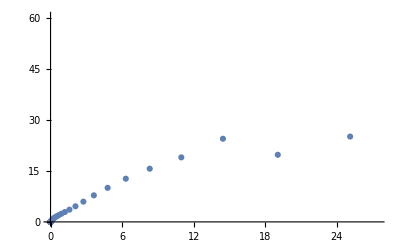

```mathematica
Inelastic
ListPlot[Elastic]
```

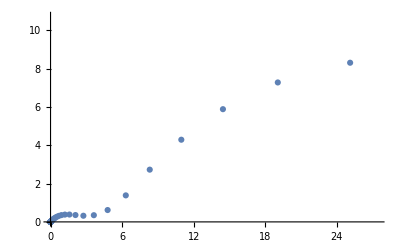

```mathematica
ListPlot[Inelastic]
```

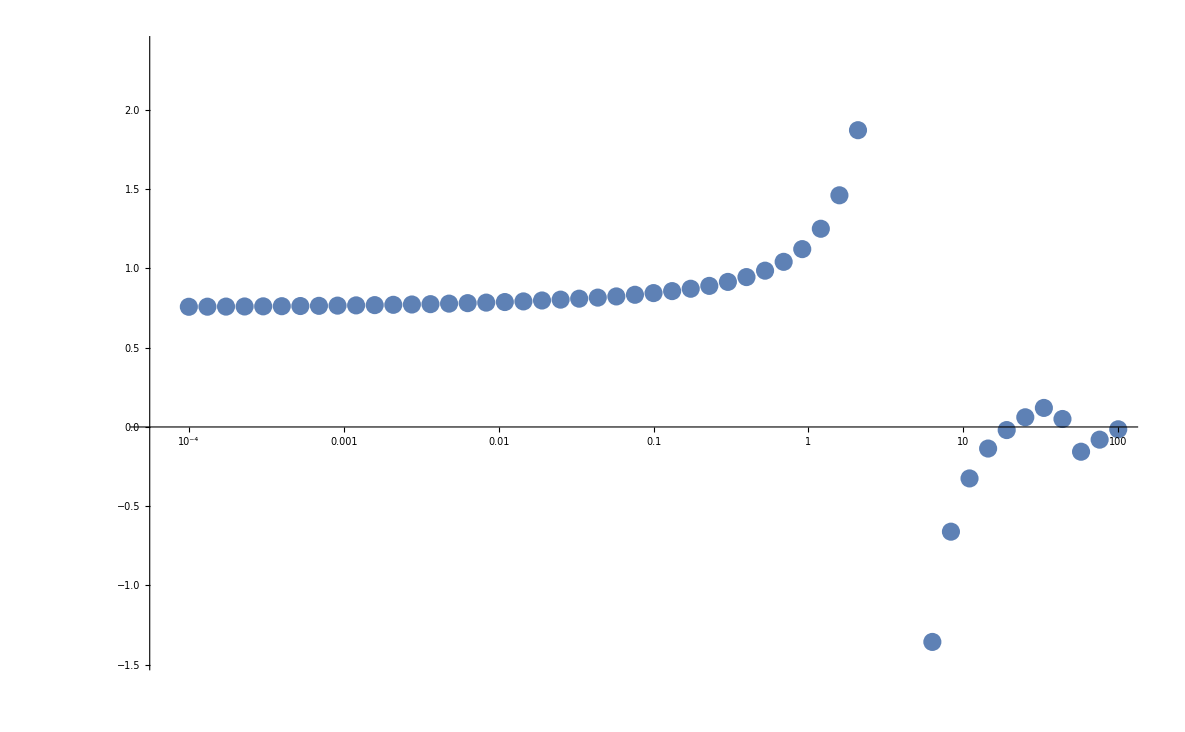

```mathematica
ListLogLinearPlot[Re[Sections]]
```

```mathematica
Re[Sections]
```

{{0.0001,0.758192},{0.000131826,0.758751},{0.00017378,0.759369},{0.000229087,0.760079},{0.000301995,0.760913},{0.000398107,0.761852},{0.000524807,0.762902},{0.000691831,0.764113},{0.000912011,0.765458},{0.00120226,0.766979},{0.00158489,0.768679},{0.0020893,0.770545},{0.00275423,0.772557},{0.00363078,0.774763},{0.0047863,0.778078},{0.00630957,0.781122},{0.00831764,0.784466},{0.0109648,0.788111},{0.0144544,0.792033},{0.0190546,0.797864},{0.0251189,0.803279},{0.0331131,0.809316},{0.0436516,0.816019},{0.057544,0.823479},{0.0758578,0.833881},{0.1,0.844521},{0.131826,0.857023},{0.17378,0.871926},{0.229087,0.889992},{0.301995,0.91508},{0.398107,0.9455},{0.524807,0.985967},{0.691831,1.04172},{0.912011,1.1219},{1.20226,1.25037},{1.58489,1.46145},{2.0893,1.8721},{2.75423,2.95162},{3.63078,11.8239},{4.7863,-3.83963},{6.30957,-1.35603},{8.31764,-0.660532},{10.9648,-0.324679},{14.4544,-0.136108},{19.0546,-0.0195552},{25.1189,0.0610449},{33.1131,0.120131},{43.6516,0.0503153},{57.544,-0.156178},{75.8578,-0.0800751},{100.,-0.0146771}}

Imports

```mathematica
scat=Range[-3.5,1.5,0.0011];
scat=1/scat;
```

Calculations

```mathematica
Elastic={};Inelastic={}; Sections={};Scattered={};
en = 0.0000001;
Print["Progress:"];
Print[ProgressIndicator[Dynamic[k],{1,Length[scat]}]];
Do[aS=scat[[i]];
k=i;
(*Print["as = ",aS];*)

xi=0.1;
(*Determines the final point of integration*)
xf=200;

(* Subroutine determining steps *)
Module[{eig,h,dbl,n,pxi,pxf,dp,x,p,tab},

pxi=Log[xi ];
pxf=Log[xf +dxf];
dp=(pxf-pxi)/nptl;
tab=Table[x=Exp[p];eig=Eigenvalues[V[x]];{x,Min[2Pi/Sqrt[Abs[en-eig]]]},{p,pxi,pxf,dp}];
lambda=Interpolation[tab]; (*Local de Broglie wavelength (minimum over all channels). Used for determination of the step size *)

xt={};
h=lambda[xi]/npt;
AppendTo[xt,xi];
AppendTo[xt,xi+h];
dbl=1; (* dbl = 1 - step doubling or halving was done in the previous step, dbl = 0 otherwise *)
n=2;

While[(xt[[n]]<xf)||(dbl==1),
Which[
(lambda[xt[[n]]]≥2 npt h)&&(dbl==0),

h=2h;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

(lambda[xt[[n]]]<npt h)&&(dbl==0),

h=h/2;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

True,


AppendTo[xt,xt[[n]]+h];
dbl=0;
];
n++;
];
nstep=n;  (* Total number of steps *);
];
(*Print["nstep = ",nstep];*)
QT=Table[en Id-V[xt[[n]]],{n,1,Length[xt]}];
phi=φ/.Solve[aS==ash[φ],φ][[1]];
Kmatr=KMatrix[en,Sin[phi],Cos[phi]];
Smatr=(Id+ⅈ Kmatr).Inverse[Id-ⅈ Kmatr];
S0 = N[Smatr[[1,1]]];
a0 = 1/(ⅈ Sqrt[en])(1-S0)/(1+S0);

(*totinelS=Pi Sum[1-Abs[Smatr[[n1,n1]]]^2,{n1,1,1}]/en;
totelS=Pi Sum[Abs[1-Smatr[[n1,n1]]]^2,{n1,1,1}]/en;*)
(*Print[a0];*)
totInEl= Sum[(2TabCh[[n1,1]]+1)(1-Abs[Smatr[[n1,n1]]]^2),{n1,1,Nch}];
totEl=  Sum[(2TabCh[[n1,1]]+1)Abs[1-Smatr[[n1,n1]]]^2,{n1,1,Nch}];

AppendTo[Elastic,{en,totEl}];
AppendTo[Inelastic,{en,totInEl}];
AppendTo[Sections,Re[a0]];
AppendTo[Scattered,{1/aS,1/Re[a0]}];

Clear[xt,QT];
,{i,1,Length[scat]}
]
```

Progress:

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.0151819,0.,0.0070768,0.,-0.0591071,0.,-0.744096,0.,-7.9559,0.,«11»},{0.,-0.411054,0.,1.04032,0.,3.09522,0.,18.2446,0.,131.118,«11»},{9.29533×10^-6,0.,-32.7299,0.,75.916,0.,199.902,0.,1084.28,0.,«11»},{0.,0.000274467,0.,-3645.5,0.,8145.87,0.,19850.3,0.,101834.,«11»},{-8.76988×10^-9,0.,0.00857348,0.,-522024.,0.,1.14504×10^6,0.,2.64028×10^6,0.,«11»},{0.,5.1227×10^-8,0.,0.510977,0.,-9.13644×10^7,0.,1.98539×10^8,0.,4.38778×10^8,«11»},{-4.40709×10^-12,0.,9.01159×10^-7,0.,45.7045,0.,-1.88983×10^10,0.,4.08954×10^10,0.,«11»},{0.,8.34442×10^-12,0.,0.0000344092,0.,5486.15,0.,-4.51052×10^12,0.,9.75092×10^12,«11»},{-9.54944×10^-16,0.,9.90543×10^-11,0.,0.00213562,0.,828684.,0.,-1.22011×10^15,0.,«11»},{0.,9.29336×10^-16,0.,2.7355×10^-9,0.,0.187885,0.,1.51095×10^8,0.,-3.68882×10^17,«11»},«11»} may contain significant numerical errors.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.0150939,0.,0.00737834,0.,-0.0568313,0.,-0.724085,0.,-7.76936,0.,«11»},{0.,-0.411054,0.,1.04032,0.,3.09522,0.,18.2446,0.,131.118,«11»},{9.69145×10^-6,0.,-32.7299,0.,75.916,0.,199.902,0.,1084.28,0.,«11»},{0.,0.000274467,0.,-3645.5,0.,8145.87,0.,19850.3,0.,101834.,«11»},{-8.43223×10^-9,0.,0.00857348,0.,-522024.,0.,1.14504×10^6,0.,2.64028×10^6,0.,«11»},{0.,5.1227×10^-8,0.,0.510977,0.,-9.13644×10^7,0.,1.98539×10^8,0.,4.38778×10^8,«11»},{-4.28858×10^-12,0.,9.01159×10^-7,0.,45.7045,0.,-1.88983×10^10,0.,4.08954×10^10,0.,«11»},{0.,8.34442×10^-12,0.,0.0000344092,0.,5486.15,0.,-4.51052×10^12,0.,9.75092×10^12,«11»},{-9.32555×10^-16,0.,9.90544×10^-11,0.,0.00213562,0.,828684.,0.,-1.22011×10^15,0.,«11»},{0.,9.29336×10^-16,0.,2.7355×10^-9,0.,0.187885,0.,1.51095×10^8,0.,-3.68882×10^17,«11»},«11»} may contain significant numerical errors.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.0150082,0.,0.00767201,0.,-0.0546149,0.,-0.704596,0.,-7.58769,0.,«11»},{0.,-0.411054,0.,1.04032,0.,3.09522,0.,18.2446,0.,131.118,«11»},{0.0000100772,0.,-32.7299,0.,75.916,0.,199.902,0.,1084.28,0.,«11»},{0.,0.000274467,0.,-3645.5,0.,8145.87,0.,19850.3,0.,101834.,«11»},{-8.1034×10^-9,0.,0.00857348,0.,-522024.,0.,1.14504×10^6,0.,2.64028×10^6,0.,«11»},{0.,5.1227×10^-8,0.,0.510977,0.,-9.13644×10^7,0.,1.98539×10^8,0.,4.38778×10^8,«11»},{-4.17316×10^-12,0.,9.01159×10^-7,0.,45.7045,0.,-1.88983×10^10,0.,4.08954×10^10,0.,«11»},{0.,8.34442×10^-12,0.,0.0000344092,0.,5486.15,0.,-4.51052×10^12,0.,9.75092×10^12,«11»},{-9.10751×10^-16,0.,9.90545×10^-11,0.,0.00213562,0.,828684.,0.,-1.22011×10^15,0.,«11»},{0.,9.29336×10^-16,0.,2.7355×10^-9,0.,0.187885,0.,1.51095×10^8,0.,-3.68882×10^17,«11»},«11»} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

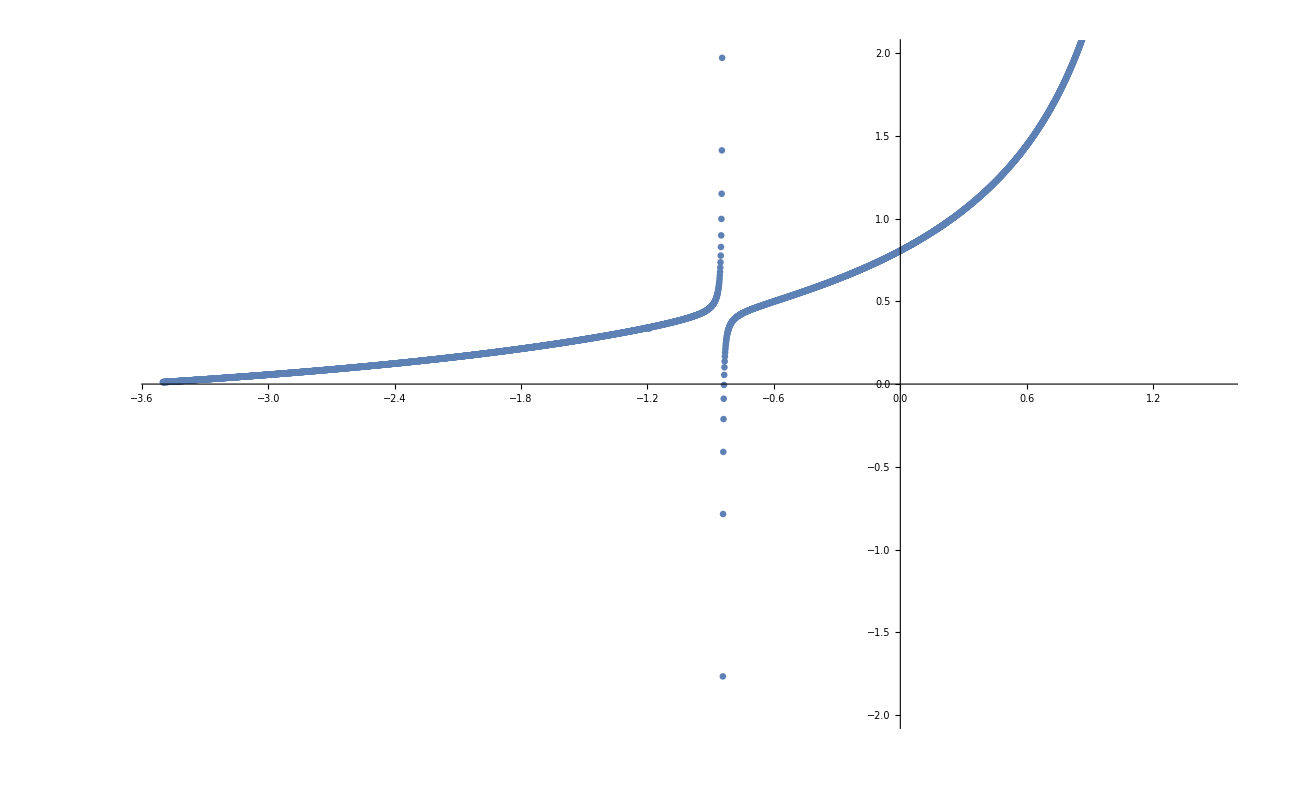

Scattered_01.csv

```mathematica
ListPlot[Re[Scattered], PlotRange->{{-3.5,1.5},{-2,2}}]
Export["Scattered_01.csv",Scattered]
```

```mathematica
Sections
```

{85.9438,85.2843,84.6346,83.9944,83.3636,82.742,82.1293,81.5254,80.9301,80.3431,79.7644,79.1938,78.631,78.0759,77.5285,76.9884,76.4556,75.9299,75.4112,74.8993,74.3941,73.8955,73.4033,72.9175,72.4378,71.9642,71.4966,71.0349,70.5789,70.1285,69.6837,69.2443,68.8102,68.3814,67.9577,67.5391,67.1254,66.7166,66.3126,65.9133,65.5186,65.1285,64.7428,64.3615,63.9846,63.6118,63.2433,62.8788,62.5184,62.1619,61.8094,61.4607,61.1157,60.7745,60.4369,60.1029,59.7725,59.4455,59.122,58.8018,58.485,58.1715,57.8611,57.5539,57.2499,56.9489,56.651,56.356,56.064,55.7748,55.4886,55.2051,54.9244,54.6464,54.3711,54.0985,53.8285,53.561,53.2961,53.0337,52.7738,52.5163,52.2612,52.0084,51.758,51.5099,51.2641,51.0205,50.7791,50.5398,50.3028,50.0678,49.8349,49.6041,49.3754,49.1486,48.9238,48.701,48.4801,48.2612,48.0441,47.8288,47.6154,47.4038,47.194,46.986,46.7797,46.5751,46.3722,46.171,45.9715,45.7735,45.5773,45.3826,45.1894,44.9979,44.8079,44.6194,44.4324,44.2469,44.0628,43.8802,43.6991,43.5194,43.341,43.1641,42.9885,42.8142,42.6413,42.4698,42.2995,42.1305,41.9628,41.7964,41.6312,41.4672,41.3045,41.1429,40.9826,40.8234,40.6654,40.5086,40.3529,40.1983,40.0449,39.8925,39.7413,39.5911,39.442,39.294,39.147,39.001,38.8561,38.7122,38.5692,38.4273,38.2864,38.1464,38.0074,37.8694,37.7322,37.5961,37.4608,37.3265,37.193,37.0605,36.9289,36.7981,36.6682,36.5391,36.411,36.2836,36.1571,36.0314,35.9066,35.7825,35.6593,35.5368,35.4152,35.2943,35.1742,35.0548,34.9362,34.8184,34.7013,34.585,34.4693,34.3544,34.2402,34.1268,34.014,33.9019,33.7905,33.6798,33.5698,33.4605,33.3518,33.2438,33.1364,33.0297,32.9236,32.8181,32.7133,32.6091,32.5055,32.4026,32.3002,32.1985,32.0973,31.9967,31.8968,31.7974,31.6985,31.6003,31.5026,31.4055,31.3089,31.2129,31.1175,31.0225,30.9282,30.8343,30.741,30.6482,30.5559,30.4642,30.3729,30.2822,30.1919,30.1022,30.013,29.9242,29.8359,29.7482,29.6609,29.574,29.4877,29.4018,29.3163,29.2314,29.1469,29.0628,28.9792,28.896,28.8133,28.731,28.6491,28.5677,28.4867,28.4062,28.326,28.2463,28.167,28.0881,28.0096,27.9315,27.8538,27.7765,27.6996,27.6231,27.547,27.4712,27.3959,27.3209,27.2463,27.1721,27.0983,27.0248,26.9517,26.879,26.8066,26.7346,26.6629,26.5916,26.5206,26.45,26.3797,26.3098,26.2402,26.171,26.1021,26.0335,25.9653,25.8973,25.8297,25.7625,25.6955,25.6289,25.5626,25.4966,25.4309,25.3655,25.3005,25.2357,25.1712,25.1071,25.0432,24.9797,24.9164,24.8534,24.7907,24.7283,24.6662,24.6044,24.5429,24.4816,24.4206,24.3599,24.2995,24.2394,24.1795,24.1199,24.0605,24.0015,23.9427,23.8841,23.8258,23.7678,23.71,23.6525,23.5952,23.5382,23.4815,23.425,23.3687,23.3127,23.2569,23.2014,23.1461,23.091,23.0362,22.9817,22.9273,22.8732,22.8193,22.7657,22.7123,22.6591,22.6061,22.5534,22.5009,22.4486,22.3965,22.3446,22.293,22.2416,22.1904,22.1394,22.0886,22.038,21.9877,21.9375,21.8876,21.8378,21.7883,21.739,21.6898,21.6409,21.5922,21.5437,21.4953,21.4472,21.3992,21.3515,21.3039,21.2566,21.2094,21.1624,21.1156,21.069,21.0225,20.9763,20.9302,20.8844,20.8387,20.7931,20.7478,20.7026,20.6576,20.6128,20.5682,20.5237,20.4794,20.4353,20.3914,20.3476,20.304,20.2606,20.2173,20.1742,20.1312,20.0885,20.0458,20.0034,19.9611,19.919,19.877,19.8352,19.7935,19.752,19.7107,19.6695,19.6284,19.5876,19.5468,19.5062,19.4658,19.4255,19.3854,19.3454,19.3056,19.2659,19.2264,19.187,19.1477,19.1086,19.0696,19.0308,18.9921,18.9536,18.9152,18.8769,18.8388,18.8008,18.7629,18.7252,18.6876,18.6502,18.6129,18.5757,18.5386,18.5017,18.4649,18.4283,18.3917,18.3553,18.3191,18.2829,18.2469,18.211,18.1752,18.1396,18.1041,18.0687,18.0334,17.9982,17.9632,17.9283,17.8935,17.8588,17.8243,17.7899,17.7555,17.7213,17.6873,17.6533,17.6194,17.5857,17.5521,17.5186,17.4852,17.4519,17.4187,17.3857,17.3527,17.3199,17.2872,17.2545,17.222,17.1896,17.1573,17.1252,17.0931,17.0611,17.0292,16.9975,16.9658,16.9342,16.9028,16.8714,16.8402,16.809,16.778,16.747,16.7162,16.6855,16.6548,16.6243,16.5938,16.5635,16.5332,16.5031,16.473,16.443,16.4132,16.3834,16.3537,16.3241,16.2946,16.2652,16.2359,16.2067,16.1776,16.1486,16.1196,16.0908,16.062,16.0334,16.0048,15.9763,15.9479,15.9196,15.8914,15.8632,15.8352,15.8072,15.7794,15.7516,15.7239,15.6962,15.6687,15.6413,15.6139,15.5866,15.5594,15.5323,15.5052,15.4783,15.4514,15.4246,15.3979,15.3713,15.3447,15.3183,15.2919,15.2656,15.2393,15.2132,15.1871,15.1611,15.1352,15.1093,15.0836,15.0579,15.0323,15.0067,14.9812,14.9559,14.9305,14.9053,14.8801,14.855,14.83,14.8051,14.7802,14.7554,14.7307,14.706,14.6814,14.6569,14.6324,14.6081,14.5838,14.5595,14.5354,14.5113,14.4872,14.4633,14.4394,14.4156,14.3918,14.3681,14.3445,14.3209,14.2975,14.274,14.2507,14.2274,14.2042,14.181,14.1579,14.1349,14.1119,14.089,14.0662,14.0434,14.0207,13.998,13.9755,13.9529,13.9305,13.9081,13.8858,13.8635,13.8413,13.8191,13.797,13.775,13.753,13.7311,13.7093,13.6875,13.6657,13.6441,13.6225,13.6009,13.5794,13.558,13.5366,13.5153,13.494,13.4728,13.4516,13.4305,13.4095,13.3885,13.3676,13.3467,13.3259,13.3051,13.2844,13.2638,13.2432,13.2227,13.2022,13.1817,13.1614,13.141,13.1208,13.1005,13.0804,13.0603,13.0402,13.0202,13.0002,12.9803,12.9605,12.9407,12.9209,12.9012,12.8816,12.862,12.8425,12.823,12.8035,12.7841,12.7648,12.7455,12.7262,12.707,12.6879,12.6688,12.6497,12.6307,12.6118,12.5929,12.574,12.5552,12.5364,12.5177,12.4991,12.4804,12.4619,12.4433,12.4249,12.4064,12.388,12.3697,12.3514,12.3331,12.3149,12.2968,12.2787,12.2606,12.2426,12.2246,12.2066,12.1887,12.1709,12.1531,12.1353,12.1176,12.0999,12.0823,12.0647,12.0472,12.0297,12.0122,11.9948,11.9774,11.9601,11.9428,11.9256,11.9084,11.8912,11.8741,11.857,11.8399,11.8229,11.806,11.7891,11.7722,11.7554,11.7386,11.7218,11.7051,11.6884,11.6718,11.6552,11.6386,11.6221,11.6056,11.5892,11.5728,11.5564,11.5401,11.5238,11.5075,11.4913,11.4752,11.459,11.4429,11.4269,11.4108,11.3949,11.3789,11.363,11.3471,11.3313,11.3155,11.2997,11.284,11.2683,11.2527,11.237,11.2215,11.2059,11.1904,11.1749,11.1595,11.1441,11.1287,11.1134,11.0981,11.0828,11.0676,11.0524,11.0372,11.0221,11.007,10.992,10.977,10.962,10.947,10.9321,10.9172,10.9023,10.8875,10.8727,10.858,10.8433,10.8286,10.8139,10.7993,10.7847,10.7701,10.7556,10.7411,10.7267,10.7122,10.6978,10.6835,10.6691,10.6548,10.6406,10.6263,10.6121,10.5979,10.5838,10.5697,10.5556,10.5415,10.5275,10.5135,10.4996,10.4856,10.4717,10.4579,10.444,10.4302,10.4164,10.4027,10.389,10.3753,10.3616,10.348,10.3344,10.3208,10.3073,10.2937,10.2802,10.2668,10.2534,10.24,10.2266,10.2132,10.1999,10.1866,10.1734,10.1602,10.147,10.1338,10.1206,10.1075,10.0944,10.0814,10.0683,10.0553,10.0423,10.0294,10.0164,10.0035,9.99067,9.97783,9.96501,9.95222,9.93945,9.92671,9.914,9.90131,9.88865,9.87602,9.86341,9.85083,9.83827,9.82574,9.81324,9.80076,9.78831,9.77588,9.76348,9.7511,9.73875,9.72643,9.71413,9.70185,9.6896,9.67738,9.66518,9.653,9.64085,9.62872,9.61662,9.60454,9.59249,9.58046,9.56846,9.55648,9.54453,9.53259,9.52069,9.5088,9.49694,9.48511,9.4733,9.46151,9.44974,9.438,9.42628,9.41459,9.40292,9.39127,9.37964,9.36804,9.35646,9.34491,9.33337,9.32186,9.31038,9.29891,9.28747,9.27605,9.26465,9.25328,9.24192,9.23059,9.21929,9.208,9.19674,9.18549,9.17427,9.16308,9.1519,9.14075,9.12961,9.1185,9.10741,9.09634,9.0853,9.07427,9.06327,9.05228,9.04132,9.03038,9.01946,9.00857,8.99769,8.98683,8.976,8.96518,8.95439,8.94361,8.93286,8.92213,8.91141,8.90072,8.89005,8.8794,8.86877,8.85816,8.84757,8.837,8.82645,8.81592,8.80541,8.79492,8.78445,8.77399,8.76356,8.75315,8.74276,8.73239,8.72203,8.7117,8.70138,8.69109,8.68081,8.67055,8.66032,8.6501,8.6399,8.62972,8.61955,8.60941,8.59929,8.58918,8.57909,8.56903,8.55898,8.54895,8.53893,8.52894,8.51896,8.509,8.49907,8.48914,8.47924,8.46936,8.45949,8.44964,8.43981,8.43,8.4202,8.41043,8.40067,8.39093,8.3812,8.3715,8.36181,8.35214,8.34248,8.33285,8.32323,8.31363,8.30404,8.29448,8.28493,8.2754,8.26588,8.25638,8.2469,8.23744,8.22799,8.21856,8.20915,8.19975,8.19037,8.18101,8.17166,8.16233,8.15302,8.14372,8.13444,8.12518,8.11593,8.1067,8.09748,8.08828,8.0791,8.06994,8.06079,8.05165,8.04254,8.03343,8.02435,8.01528,8.00622,7.99719,7.98816,7.97916,7.97017,7.96119,7.95223,7.94329,7.93436,7.92545,7.91655,7.90767,7.8988,7.88995,7.88111,7.87229,7.86349,7.8547,7.84592,7.83716,7.82842,7.81969,7.81097,7.80227,7.79359,7.78492,7.77626,7.76762,7.759,7.75039,7.74179,7.73321,7.72464,7.71609,7.70755,7.69903,7.69052,7.68202,7.67354,7.66508,7.65663,7.64819,7.63977,7.63136,7.62296,7.61458,7.60622,7.59787,7.58953,7.5812,7.57289,7.5646,7.55632,7.54805,7.53979,7.53155,7.52332,7.51511,7.50691,7.49873,7.49055,7.48239,7.47425,7.46612,7.458,7.44989,7.4418,7.43372,7.42566,7.41761,7.40957,7.40154,7.39353,7.38553,7.37755,7.36958,7.36162,7.35367,7.34574,7.33782,7.32991,7.32202,7.31414,7.30627,7.29841,7.29057,7.28274,7.27492,7.26712,7.25932,7.25154,7.24378,7.23602,7.22828,7.22055,7.21284,7.20513,7.19744,7.18976,7.18209,7.17444,7.1668,7.15917,7.15155,7.14394,7.13635,7.12877,7.1212,7.11364,7.1061,7.09856,7.09104,7.08353,7.07604,7.06855,7.06108,7.05362,7.04617,7.03873,7.0313,7.02389,7.01649,7.00909,7.00172,6.99435,6.98699,6.97965,6.97232,6.96499,6.95768,6.95039,6.9431,6.93582,6.92856,6.92131,6.91407,6.90684,6.89962,6.89241,6.88521,6.87803,6.87086,6.86369,6.85654,6.8494,6.84227,6.83515,6.82805,6.82095,6.81386,6.80679,6.79973,6.79267,6.78563,6.7786,6.77158,6.76457,6.75757,6.75059,6.74361,6.73664,6.72969,6.72274,6.71581,6.70888,6.70197,6.69507,6.68818,6.68129,6.67442,6.66756,6.66071,6.65387,6.64704,6.64022,6.63342,6.62662,6.61983,6.61305,6.60628,6.59953,6.59278,6.58604,6.57931,6.5726,6.56589,6.55919,6.55251,6.54583,6.53916,6.53251,6.52586,6.51922,6.5126,6.50598,6.49937,6.49278,6.48619,6.47961,6.47304,6.46649,6.45994,6.4534,6.44687,6.44035,6.43384,6.42734,6.42085,6.41437,6.4079,6.40144,6.39499,6.38854,6.38211,6.37569,6.36927,6.36287,6.35647,6.35009,6.34371,6.33734,6.33098,6.32464,6.3183,6.31197,6.30565,6.29933,6.29303,6.28674,6.28045,6.27418,6.26791,6.26166,6.25541,6.24917,6.24294,6.23672,6.23051,6.2243,6.21811,6.21193,6.20575,6.19958,6.19342,6.18728,6.18113,6.175,6.16888,6.16277,6.15666,6.15056,6.14448,6.1384,6.13233,6.12626,6.12021,6.11417,6.10813,6.1021,6.09608,6.09007,6.08407,6.07808,6.07209,6.06612,6.06015,6.05419,6.04824,6.0423,6.03636,6.03044,6.02452,6.01861,6.01271,6.00682,6.00093,5.99506,5.98919,5.98333,5.97748,5.97164,5.9658,5.95997,5.95416,5.94835,5.94254,5.93675,5.93096,5.92518,5.91941,5.91365,5.9079,5.90215,5.89641,5.89068,5.88496,5.87925,5.87354,5.86784,5.86215,5.85647,5.85079,5.84513,5.83947,5.83382,5.82817,5.82254,5.81691,5.81129,5.80567,5.80007,5.79447,5.78888,5.7833,5.77773,5.77216,5.7666,5.76105,5.7555,5.74997,5.74444,5.73892,5.7334,5.7279,5.7224,5.7169,5.71142,5.70594,5.70047,5.69501,5.68956,5.68411,5.67867,5.67324,5.66781,5.66239,5.65698,5.65158,5.64618,5.64079,5.63541,5.63004,5.62467,5.61931,5.61396,5.60861,5.60327,5.59794,5.59262,5.5873,5.58199,5.57669,5.57139,5.5661,5.56082,5.55554,5.55028,5.54502,5.53976,5.53451,5.52927,5.52404,5.51881,5.51359,5.50838,5.50318,5.49798,5.49279,5.4876,5.48242,5.47725,5.47209,5.46693,5.46178,5.45663,5.45149,5.44636,5.44124,5.43612,5.43101,5.42591,5.42081,5.41572,5.41063,5.40555,5.40048,5.39542,5.39036,5.38531,5.38026,5.37523,5.37019,5.36517,5.36015,5.35514,5.35013,5.34513,5.34014,5.33515,5.33017,5.3252,5.32023,5.31527,5.31032,5.30537,5.30043,5.29549,5.29056,5.28564,5.28072,5.27581,5.27091,5.26601,5.26112,5.25623,5.25135,5.24648,5.24161,5.23675,5.2319,5.22705,5.22221,5.21737,5.21254,5.20772,5.2029,5.19809,5.19328,5.18848,5.18369,5.1789,5.17412,5.16935,5.16458,5.15981,5.15506,5.1503,5.14556,5.14082,5.13609,5.13136,5.12664,5.12192,5.11721,5.11251,5.10781,5.10312,5.09843,5.09375,5.08908,5.08441,5.07974,5.07509,5.07044,5.06579,5.06115,5.05652,5.05189,5.04726,5.04265,5.03804,5.03343,5.02883,5.02424,5.01965,5.01506,5.01049,5.00591,5.00135,4.99679,4.99223,4.98768,4.98314,4.9786,4.97407,4.96954,4.96502,4.9605,4.95599,4.95149,4.94699,4.94249,4.938,4.93352,4.92904,4.92457,4.9201,4.91564,4.91119,4.90674,4.90229,4.89785,4.89342,4.88899,4.88456,4.88014,4.87573,4.87132,4.86692,4.86252,4.85813,4.85375,4.84936,4.84499,4.84062,4.83625,4.83189,4.82754,4.82319,4.81884,4.8145,4.81017,4.80584,4.80151,4.79719,4.79288,4.78857,4.78427,4.77997,4.77568,4.77139,4.7671,4.76283,4.75855,4.75428,4.75002,4.74576,4.74151,4.73726,4.73302,4.72878,4.72455,4.72032,4.7161,4.71188,4.70767,4.70346,4.69926,4.69506,4.69086,4.68668,4.68249,4.67831,4.67414,4.66997,4.66581,4.66165,4.65749,4.65334,4.6492,4.64506,4.64092,4.63679,4.63267,4.62855,4.62443,4.62032,4.61622,4.61211,4.60802,4.60392,4.59984,4.59575,4.59168,4.5876,4.58353,4.57947,4.57541,4.57136,4.56731,4.56326,4.55922,4.55519,4.55115,4.54713,4.5431,4.53909,4.53507,4.53107,4.52706,4.52306,4.51907,4.51508,4.51109,4.50711,4.50313,4.49916,4.49519,4.49123,4.48727,4.48332,4.47937,4.47542,4.47148,4.46755,4.46362,4.45969,4.45577,4.45185,4.44793,4.44402,4.44012,4.43622,4.43232,4.42843,4.42454,4.42066,4.41678,4.4129,4.40903,4.40517,4.4013,4.39745,4.39359,4.38974,4.3859,4.38206,4.37822,4.37439,4.37056,4.36674,4.36292,4.35911,4.3553,4.35149,4.34769,4.34389,4.3401,4.33631,4.33252,4.32874,4.32496,4.32119,4.31742,4.31366,4.3099,4.30614,4.30239,4.29864,4.29489,4.29115,4.28742,4.28369,4.27996,4.27624,4.27252,4.2688,4.26509,4.26138,4.25768,4.25398,4.25028,4.24659,4.2429,4.23922,4.23554,4.23187,4.22819,4.22453,4.22086,4.2172,4.21355,4.2099,4.20625,4.20261,4.19897,4.19533,4.1917,4.18807,4.18445,4.18082,4.17721,4.1736,4.16999,4.16638,4.16278,4.15918,4.15559,4.152,4.14842,4.14483,4.14126,4.13768,4.13411,4.13054,4.12698,4.12342,4.11987,4.11631,4.11277,4.10922,4.10568,4.10215,4.09861,4.09508,4.09156,4.08804,4.08452,4.081,4.07749,4.07399,4.07048,4.06698,4.06349,4.06,4.05651,4.05302,4.04954,4.04606,4.04259,4.03912,4.03565,4.03219,4.02873,4.02527,4.02182,4.01837,4.01493,4.01148,4.00805,4.00461,4.00118,3.99775,3.99433,3.99091,3.98749,3.98408,3.98067,3.97726,3.97386,3.97046,3.96706,3.96367,3.96028,3.9569,3.95352,3.95014,3.94676,3.94339,3.94002,3.93666,3.9333,3.92994,3.92658,3.92323,3.91988,3.91654,3.9132,3.90986,3.90653,3.9032,3.89987,3.89655,3.89323,3.88991,3.88659,3.88328,3.87998,3.87667,3.87337,3.87007,3.86678,3.86349,3.8602,3.85692,3.85364,3.85036,3.84708,3.84381,3.84055,3.83728,3.83402,3.83076,3.82751,3.82426,3.82101,3.81776,3.81452,3.81128,3.80805,3.80481,3.80158,3.79836,3.79514,3.79192,3.7887,3.78549,3.78228,3.77907,3.77587,3.77266,3.76947,3.76627,3.76308,3.75989,3.75671,3.75353,3.75035,3.74717,3.744,3.74083,3.73766,3.7345,3.73134,3.72818,3.72503,3.72188,3.71873,3.71558,3.71244,3.7093,3.70617,3.70303,3.6999,3.69678,3.69365,3.69053,3.68741,3.6843,3.68119,3.67808,3.67497,3.67187,3.66877,3.66567,3.66258,3.65949,3.6564,3.65331,3.65023,3.64715,3.64407,3.641,3.63793,3.63486,3.63179,3.62873,3.62567,3.62262,3.61956,3.61651,3.61346,3.61042,3.60738,3.60434,3.6013,3.59827,3.59524,3.59221,3.58918,3.58616,3.58314,3.58012,3.57711,3.5741,3.57109,3.56808,3.56508,3.56208,3.55908,3.55609,3.5531,3.55011,3.54712,3.54414,3.54116,3.53818,3.5352,3.53223,3.52926,3.52629,3.52333,3.52037,3.51741,3.51445,3.5115,3.50855,3.5056,3.50265,3.49971,3.49677,3.49383,3.49089,3.48796,3.48503,3.4821,3.47918,3.47626,3.47334,3.47042,3.46751,3.46459,3.46168,3.45878,3.45587,3.45297,3.45007,3.44718,3.44428,3.44139,3.4385,3.43562,3.43273,3.42985,3.42697,3.4241,3.42122,3.41835,3.41548,3.41262,3.40975,3.40689,3.40403,3.40118,3.39832,3.39547,3.39262,3.38978,3.38693,3.38409,3.38125,3.37842,3.37558,3.37275,3.36992,3.36709,3.36427,3.36145,3.35863,3.35581,3.35299,3.35018,3.34737,3.34456,3.34176,3.33895,3.33615,3.33336,3.33056,3.32777,3.32497,3.32218,3.3194,3.31661,3.31383,3.31105,3.30827,3.3055,3.30272,3.29995,3.29718,3.29442,3.29165,3.28889,3.28613,3.28337,3.28062,3.27787,3.27512,3.27237,3.26962,3.26688,3.26414,3.2614,3.25866,3.25592,3.25319,3.25046,3.24773,3.245,3.24228,3.23956,3.23684,3.23412,3.2314,3.22869,3.22598,3.22327,3.22056,3.21785,3.21515,3.21245,3.20975,3.20705,3.20436,3.20166,3.19897,3.19628,3.1936,3.19091,3.18823,3.18555,3.18287,3.18019,3.17752,3.17484,3.17217,3.1695,3.16684,3.16417,3.16151,3.15885,3.15619,3.15353,3.15088,3.14822,3.14557,3.14292,3.14027,3.13763,3.13498,3.13234,3.1297,3.12706,3.12443,3.12179,3.11916,3.11653,3.1139,3.11127,3.10864,3.10602,3.1034,3.10078,3.09816,3.09554,3.09293,3.09031,3.0877,3.08509,3.08248,3.07988,3.07727,3.07467,3.07206,3.06946,3.06687,3.06427,3.06167,3.05908,3.05649,3.0539,3.05131,3.04872,3.04613,3.04355,3.04096,3.03838,3.0358,3.03322,3.03064,3.02807,3.02549,3.02291,3.02034,3.01777,3.0152,3.01263,3.01006,3.00749,3.00492,3.00236,2.99979,2.99722,2.99466,2.99209,2.98953,2.98696,2.9844,2.98183,2.97926,2.9767,2.97413,2.97156,2.96898,2.9664,2.96382,2.96123,2.95863,2.95603,2.95341,2.95077,2.94811,2.94541,2.94266,2.93984,2.93689,2.93372,2.93009,2.92521,2.91449,2.98909,2.93435,2.92726,2.92304,2.91963,2.91658,2.9137,2.91093,2.90822,2.90556,2.90294,2.90033,2.89775,2.89517,2.89261,2.89006,2.88752,2.88499,2.88246,2.87993,2.87741,2.8749,2.87238,2.86987,2.86737,2.86486,2.86236,2.85986,2.85737,2.85487,2.85238,2.84989,2.8474,2.84491,2.84242,2.83993,2.83745,2.83497,2.83249,2.83,2.82753,2.82505,2.82257,2.82009,2.81762,2.81514,2.81267,2.8102,2.80773,2.80525,2.80278,2.80032,2.79785,2.79538,2.79291,2.79044,2.78798,2.78551,2.78305,2.78058,2.77812,2.77565,2.77319,2.77073,2.76827,2.7658,2.76334,2.76088,2.75842,2.75596,2.7535,2.75104,2.74858,2.74612,2.74366,2.7412,2.73874,2.73628,2.73382,2.73136,2.7289,2.72644,2.72398,2.72152,2.71906,2.7166,2.71414,2.71168,2.70921,2.70675,2.70429,2.70183,2.69937,2.6969,2.69444,2.69197,2.68951,2.68704,2.68458,2.68211,2.67964,2.67718,2.67471,2.67224,2.66977,2.6673,2.66482,2.66235,2.65988,2.6574,2.65492,2.65245,2.64997,2.64749,2.64501,2.64252,2.64004,2.63756,2.63507,2.63258,2.63009,2.6276,2.62511,2.62261,2.62011,2.61762,2.61511,2.61261,2.61011,2.6076,2.60509,2.60258,2.60007,2.59755,2.59503,2.59251,2.58999,2.58747,2.58494,2.58241,2.57987,2.57734,2.5748,2.57225,2.56971,2.56716,2.5646,2.56205,2.55949,2.55693,2.55436,2.55179,2.54921,2.54663,2.54405,2.54146,2.53887,2.53628,2.53368,2.53107,2.52846,2.52585,2.52323,2.5206,2.51797,2.51534,2.5127,2.51005,2.5074,2.50474,2.50207,2.4994,2.49673,2.49404,2.49135,2.48865,2.48595,2.48324,2.48052,2.47779,2.47505,2.47231,2.46956,2.4668,2.46403,2.46125,2.45846,2.45567,2.45286,2.45005,2.44722,2.44438,2.44153,2.43868,2.43581,2.43292,2.43003,2.42713,2.42421,2.42128,2.41833,2.41537,2.4124,2.40941,2.40641,2.4034,2.40036,2.39732,2.39425,2.39117,2.38807,2.38495,2.38181,2.37866,2.37548,2.37229,2.36907,2.36583,2.36257,2.35929,2.35599,2.35265,2.3493,2.34592,2.34251,2.33907,2.33561,2.33212,2.32859,2.32504,2.32145,2.31783,2.31417,2.31048,2.30675,2.30298,2.29918,2.29533,2.29144,2.2875,2.28352,2.2795,2.27542,2.27129,2.26711,2.26287,2.25858,2.25422,2.2498,2.24532,2.24077,2.23615,2.23146,2.22669,2.22184,2.21691,2.21189,2.20678,2.20158,2.19627,2.19087,2.18535,2.17971,2.17396,2.16808,2.16207,2.15591,2.14961,2.14316,2.13654,2.12974,2.12277,2.11559,2.10822,2.10063,2.0928,2.08473,2.0764,2.06779,2.05889,2.04966,2.0401,2.03018,2.01986,2.00912,1.99793,1.98626,1.97405,1.96128,1.94788,1.93381,1.91901,1.90339,1.8869,1.86943,1.85089,1.83116,1.81012,1.7876,1.76344,1.73742,1.70931,1.67883,1.64563,1.6093,1.56937,1.52522,1.47611,1.42113,1.35909,1.2885,1.2074,1.11317,1.00225,0.869678,0.708289,0.507377,0.250178,-0.0911076,-0.5662,-1.27364,-2.44019,-4.73001,-11.2813,-195.307,18.0445,9.86744,7.27801,6.00672,5.25082,4.74942,4.39229,4.12481,3.91686,3.75044,3.61416,3.50044,3.40403,3.32121,3.24924,3.18609,3.13019,3.08033,3.03555,2.99509,2.95832,2.92474,2.89394,2.86557,2.83933,2.81498,2.7923,2.77113,2.75129,2.73267,2.71513,2.69858,2.68294,2.66811,2.65403,2.64063,2.62787,2.61569,2.60405,2.5929,2.58221,2.57195,2.56208,2.55259,2.54344,2.53461,2.52609,2.51785,2.50988,2.50216,2.49467,2.48741,2.48035,2.4735,2.46683,2.46034,2.45401,2.44785,2.44184,2.43597,2.43024,2.42464,2.41916,2.4138,2.40856,2.40342,2.39838,2.39345,2.38861,2.38385,2.37919,2.37461,2.3701,2.36568,2.36133,2.35705,2.35283,2.34868,2.3446,2.34057,2.33661,2.3327,2.32884,2.32504,2.32129,2.31758,2.31393,2.31031,2.30675,2.30322,2.29974,2.2963,2.2929,2.28953,2.2862,2.2829,2.27964,2.27642,2.27322,2.27006,2.26693,2.26382,2.26075,2.2577,2.25469,2.25169,2.24873,2.24578,2.24287,2.23997,2.2371,2.23425,2.23143,2.22862,2.22584,2.22308,2.22034,2.21761,2.21491,2.21222,2.20955,2.2069,2.20427,2.20165,2.19906,2.19647,2.1939,2.19135,2.18882,2.18629,2.18379,2.18129,2.17881,2.17635,2.17389,2.17145,2.16903,2.16661,2.16421,2.16182,2.15944,2.15708,2.15472,2.15238,2.15005,2.14772,2.14541,2.14311,2.14082,2.13854,2.13627,2.13401,2.13175,2.12951,2.12728,2.12505,2.12284,2.12063,2.11843,2.11624,2.11406,2.11189,2.10972,2.10756,2.10541,2.10327,2.10113,2.09901,2.09689,2.09477,2.09267,2.09057,2.08848,2.08639,2.08431,2.08224,2.08018,2.07812,2.07606,2.07402,2.07198,2.06994,2.06791,2.06589,2.06387,2.06186,2.05986,2.05786,2.05586,2.05387,2.05189,2.04991,2.04794,2.04597,2.04401,2.04205,2.0401,2.03815,2.03621,2.03427,2.03234,2.03041,2.02848,2.02656,2.02465,2.02274,2.02083,2.01893,2.01703,2.01514,2.01325,2.01137,2.00949,2.00761,2.00574,2.00387,2.00201,2.00015,1.99829,1.99644,1.99459,1.99274,1.9909,1.98906,1.98723,1.9854,1.98357,1.98175,1.97993,1.97811,1.9763,1.97449,1.97269,1.97088,1.96909,1.96729,1.9655,1.96371,1.96192,1.96014,1.95836,1.95658,1.95481,1.95304,1.95127,1.94951,1.94775,1.94599,1.94423,1.94248,1.94073,1.93898,1.93724,1.9355,1.93376,1.93202,1.93029,1.92856,1.92683,1.92511,1.92339,1.92167,1.91995,1.91824,1.91653,1.91482,1.91311,1.91141,1.90971,1.90801,1.90631,1.90462,1.90293,1.90124,1.89956,1.89787,1.89619,1.89451,1.89283,1.89116,1.88949,1.88782,1.88615,1.88449,1.88282,1.88116,1.87951,1.87785,1.8762,1.87454,1.87289,1.87125,1.8696,1.86796,1.86632,1.86468,1.86304,1.86141,1.85978,1.85815,1.85652,1.85489,1.85327,1.85165,1.85002,1.84841,1.84679,1.84518,1.84356,1.84195,1.84035,1.83874,1.83714,1.83553,1.83393,1.83233,1.83074,1.82914,1.82755,1.82596,1.82437,1.82278,1.82119,1.81961,1.81803,1.81645,1.81487,1.81329,1.81172,1.81015,1.80857,1.807,1.80544,1.80387,1.80231,1.80074,1.79918,1.79762,1.79607,1.79451,1.79296,1.7914,1.78985,1.7883,1.78676,1.78521,1.78366,1.78212,1.78058,1.77904,1.7775,1.77597,1.77443,1.7729,1.77137,1.76984,1.76831,1.76678,1.76526,1.76373,1.76221,1.76069,1.75917,1.75766,1.75614,1.75462,1.75311,1.7516,1.75009,1.74858,1.74707,1.74557,1.74406,1.74256,1.74106,1.73956,1.73806,1.73657,1.73507,1.73358,1.73208,1.73059,1.7291,1.72762,1.72613,1.72464,1.72316,1.72168,1.72019,1.71871,1.71724,1.71576,1.71428,1.71281,1.71134,1.70986,1.70839,1.70692,1.70546,1.70399,1.70253,1.70106,1.6996,1.69814,1.69668,1.69522,1.69376,1.69231,1.69085,1.6894,1.68795,1.6865,1.68505,1.6836,1.68215,1.68071,1.67926,1.67782,1.67638,1.67494,1.6735,1.67206,1.67062,1.66919,1.66775,1.66632,1.66489,1.66346,1.66203,1.6606,1.65917,1.65775,1.65632,1.6549,1.65348,1.65206,1.65064,1.64922,1.6478,1.64638,1.64497,1.64356,1.64214,1.64073,1.63932,1.63791,1.6365,1.6351,1.63369,1.63229,1.63088,1.62948,1.62808,1.62668,1.62528,1.62388,1.62249,1.62109,1.6197,1.6183,1.61691,1.61552,1.61413,1.61274,1.61136,1.60997,1.60858,1.6072,1.60582,1.60443,1.60305,1.60167,1.60029,1.59892,1.59754,1.59616,1.59479,1.59342,1.59204,1.59067,1.5893,1.58793,1.58657,1.5852,1.58383,1.58247,1.5811,1.57974,1.57838,1.57702,1.57566,1.5743,1.57294,1.57158,1.57023,1.56887,1.56752,1.56617,1.56482,1.56347,1.56212,1.56077,1.55942,1.55808,1.55673,1.55539,1.55404,1.5527,1.55136,1.55002,1.54868,1.54734,1.546,1.54467,1.54333,1.542,1.54066,1.53933,1.538,1.53667,1.53534,1.53401,1.53268,1.53136,1.53003,1.52871,1.52738,1.52606,1.52474,1.52342,1.5221,1.52078,1.51946,1.51814,1.51683,1.51551,1.5142,1.51288,1.51157,1.51026,1.50895,1.50764,1.50633,1.50502,1.50372,1.50241,1.5011,1.4998,1.4985,1.4972,1.49589,1.49459,1.49329,1.492,1.4907,1.4894,1.48811,1.48681,1.48552,1.48422,1.48293,1.48164,1.48035,1.47906,1.47777,1.47648,1.4752,1.47391,1.47263,1.47134,1.47006,1.46878,1.46749,1.46621,1.46493,1.46366,1.46238,1.4611,1.45982,1.45855,1.45727,1.456,1.45473,1.45346,1.45218,1.45091,1.44964,1.44838,1.44711,1.44584,1.44458,1.44331,1.44205,1.44078,1.43952,1.43826,1.437,1.43574,1.43448,1.43322,1.43196,1.43071,1.42945,1.42819,1.42694,1.42569,1.42443,1.42318,1.42193,1.42068,1.41943,1.41818,1.41694,1.41569,1.41444,1.4132,1.41195,1.41071,1.40947,1.40823,1.40698,1.40574,1.40451,1.40327,1.40203,1.40079,1.39956,1.39832,1.39708,1.39585,1.39462,1.39339,1.39215,1.39092,1.38969,1.38846,1.38724,1.38601,1.38478,1.38356,1.38233,1.38111,1.37988,1.37866,1.37744,1.37622,1.37499,1.37377,1.37256,1.37134,1.37012,1.3689,1.36769,1.36647,1.36526,1.36404,1.36283,1.36162,1.36041,1.3592,1.35799,1.35678,1.35557,1.35436,1.35316,1.35195,1.35074,1.34954,1.34833,1.34713,1.34593,1.34473,1.34353,1.34233,1.34113,1.33993,1.33873,1.33753,1.33634,1.33514,1.33395,1.33275,1.33156,1.33037,1.32917,1.32798,1.32679,1.3256,1.32441,1.32322,1.32204,1.32085,1.31966,1.31848,1.31729,1.31611,1.31492,1.31374,1.31256,1.31138,1.3102,1.30902,1.30784,1.30666,1.30548,1.30431,1.30313,1.30195,1.30078,1.2996,1.29843,1.29726,1.29609,1.29491,1.29374,1.29257,1.2914,1.29024,1.28907,1.2879,1.28673,1.28557,1.2844,1.28324,1.28207,1.28091,1.27975,1.27859,1.27743,1.27627,1.27511,1.27395,1.27279,1.27163,1.27047,1.26932,1.26816,1.26701,1.26585,1.2647,1.26354,1.26239,1.26124,1.26009,1.25894,1.25779,1.25664,1.25549,1.25434,1.2532,1.25205,1.25091,1.24976,1.24862,1.24747,1.24633,1.24519,1.24404,1.2429,1.24176,1.24062,1.23948,1.23835,1.23721,1.23607,1.23493,1.2338,1.23266,1.23153,1.23039,1.22926,1.22813,1.22699,1.22586,1.22473,1.2236,1.22247,1.22134,1.22022,1.21909,1.21796,1.21683,1.21571,1.21458,1.21346,1.21233,1.21121,1.21009,1.20897,1.20784,1.20672,1.2056,1.20448,1.20337,1.20225,1.20113,1.20001,1.1989,1.19778,1.19666,1.19555,1.19444,1.19332,1.19221,1.1911,1.18999,1.18887,1.18776,1.18665,1.18555,1.18444,1.18333,1.18222,1.18111,1.18001,1.1789,1.1778,1.17669,1.17559,1.17449,1.17338,1.17228,1.17118,1.17008,1.16898,1.16788,1.16678,1.16568,1.16458,1.16349,1.16239,1.16129,1.1602,1.1591,1.15801,1.15692,1.15582,1.15473,1.15364,1.15255,1.15145,1.15036,1.14927,1.14819,1.1471,1.14601,1.14492,1.14383,1.14275,1.14166,1.14058,1.13949,1.13841,1.13733,1.13624,1.13516,1.13408,1.133,1.13192,1.13084,1.12976,1.12868,1.1276,1.12652,1.12544,1.12437,1.12329,1.12222,1.12114,1.12007,1.11899,1.11792,1.11685,1.11577,1.1147,1.11363,1.11256,1.11149,1.11042,1.10935,1.10828,1.10721,1.10615,1.10508,1.10401,1.10295,1.10188,1.10082,1.09975,1.09869,1.09763,1.09657,1.0955,1.09444,1.09338,1.09232,1.09126,1.0902,1.08914,1.08808,1.08703,1.08597,1.08491,1.08386,1.0828,1.08175,1.08069,1.07964,1.07858,1.07753,1.07648,1.07543,1.07437,1.07332,1.07227,1.07122,1.07017,1.06912,1.06808,1.06703,1.06598,1.06493,1.06389,1.06284,1.0618,1.06075,1.05971,1.05866,1.05762,1.05658,1.05553,1.05449,1.05345,1.05241,1.05137,1.05033,1.04929,1.04825,1.04721,1.04618,1.04514,1.0441,1.04307,1.04203,1.041,1.03996,1.03893,1.03789,1.03686,1.03583,1.03479,1.03376,1.03273,1.0317,1.03067,1.02964,1.02861,1.02758,1.02655,1.02553,1.0245,1.02347,1.02244,1.02142,1.02039,1.01937,1.01834,1.01732,1.01629,1.01527,1.01425,1.01323,1.0122,1.01118,1.01016,1.00914,1.00812,1.0071,1.00608,1.00507,1.00405,1.00303,1.00201,1.001,0.99998,0.998965,0.997949,0.996935,0.99592,0.994907,0.993893,0.99288,0.991868,0.990856,0.989844,0.988833,0.987823,0.986812,0.985803,0.984793,0.983784,0.982776,0.981768,0.980761,0.979754,0.978747,0.977741,0.976735,0.97573,0.974725,0.973721,0.972717,0.971713,0.97071,0.969708,0.968706,0.967704,0.966703,0.965702,0.964702,0.963702,0.962702,0.961703,0.960704,0.959706,0.958708,0.957711,0.956714,0.955718,0.954722,0.953726,0.952731,0.951736,0.950742,0.949748,0.948754,0.947761,0.946769,0.945776,0.944785,0.943793,0.942802,0.941812,0.940822,0.939832,0.938843,0.937854,0.936865,0.935877,0.93489,0.933902,0.932916,0.931929,0.930943,0.929958,0.928973,0.927988,0.927004,0.92602,0.925036,0.924053,0.923071,0.922088,0.921106,0.920125,0.919144,0.918163,0.917183,0.916203,0.915224,0.914245,0.913266,0.912288,0.91131,0.910332,0.909355,0.908379,0.907402,0.906426,0.905451,0.904476,0.903501,0.902527,0.901553,0.900579,0.899606,0.898634,0.897661,0.896689,0.895718,0.894746,0.893775,0.892805,0.891835,0.890865,0.889896,0.888927,0.887959,0.88699,0.886023,0.885055,0.884088,0.883121,0.882155,0.881189,0.880224,0.879259,0.878294,0.877329,0.876365,0.875402,0.874438,0.873475,0.872513,0.871551,0.870589,0.869627,0.868666,0.867705,0.866745,0.865785,0.864825,0.863866,0.862907,0.861949,0.86099,0.860032,0.859075,0.858118,0.857161,0.856205,0.855248,0.854293,0.853337,0.852382,0.851428,0.850473,0.849519,0.848566,0.847612,0.846659,0.845707,0.844755,0.843803,0.842851,0.8419,0.840949,0.839999,0.839048,0.838098,0.837149,0.8362,0.835251,0.834302,0.833354,0.832406,0.831459,0.830512,0.829565,0.828618,0.827672,0.826726,0.825781,0.824836,0.823891,0.822946,0.822002,0.821058,0.820115,0.819172,0.818229,0.817286,0.816344,0.815402,0.81446,0.813519,0.812578,0.811637,0.810697,0.809757,0.808817,0.807878,0.806939,0.806,0.805062,0.804124,0.803186,0.802248,0.801311,0.800374,0.799438,0.798501,0.797565,0.79663,0.795694,0.794759,0.793824,0.79289,0.791956,0.791022,0.790088,0.789155,0.788222,0.78729,0.786357,0.785425,0.784493,0.783562,0.782631,0.7817,0.780769,0.779839,0.778909,0.777979,0.77705,0.776121,0.775192,0.774263,0.773335,0.772407,0.771479,0.770552,0.769624,0.768698,0.767771,0.766845,0.765919,0.764993,0.764067,0.763142,0.762217,0.761292,0.760368,0.759444,0.75852,0.757596,0.756673,0.75575,0.754827,0.753905,0.752983,0.752061,0.751139,0.750217,0.749296,0.748375,0.747455,0.746534,0.745614,0.744694,0.743775,0.742855,0.741936,0.741017,0.740099,0.73918,0.738262,0.737344,0.736427,0.735509,0.734592,0.733675,0.732759,0.731842,0.730926,0.73001,0.729095,0.728179,0.727264,0.726349,0.725435,0.72452,0.723606,0.722692,0.721778,0.720865,0.719952,0.719039,0.718126,0.717213,0.716301,0.715389,0.714477,0.713566,0.712654,0.711743,0.710832,0.709921,0.709011,0.708101,0.707191,0.706281,0.705371,0.704462,0.703553,0.702644,0.701735,0.700826,0.699918,0.69901,0.698102,0.697194,0.696287,0.69538,0.694473,0.693566,0.692659,0.691753,0.690847,0.689941,0.689035,0.688129,0.687224,0.686319,0.685414,0.684509,0.683604,0.6827,0.681796,0.680892,0.679988,0.679084,0.678181,0.677277,0.676374,0.675471,0.674569,0.673666,0.672764,0.671862,0.67096,0.670058,0.669156,0.668255,0.667354,0.666453,0.665552,0.664651,0.663751,0.66285,0.66195,0.66105,0.66015,0.659251,0.658351,0.657452,0.656553,0.655654,0.654755,0.653856,0.652958,0.652059,0.651161,0.650263,0.649365,0.648468,0.64757,0.646673,0.645776,0.644878,0.643982,0.643085,0.642188,0.641292,0.640395,0.639499,0.638603,0.637707,0.636811,0.635916,0.63502,0.634125,0.63323,0.632335,0.63144,0.630545,0.62965,0.628756,0.627862,0.626967,0.626073,0.625179,0.624285,0.623392,0.622498,0.621604,0.620711,0.619818,0.618925,0.618032,0.617139,0.616246,0.615353,0.614461,0.613569,0.612676,0.611784,0.610892,0.61,0.609108,0.608216,0.607325,0.606433,0.605542,0.60465,0.603759,0.602868,0.601977,0.601086,0.600195,0.599304,0.598414,0.597523,0.596633,0.595742,0.594852,0.593962,0.593072,0.592182,0.591292,0.590402,0.589512,0.588622,0.587732,0.586843,0.585953,0.585064,0.584175,0.583285,0.582396,0.581507,0.580618,0.579729,0.57884,0.577951,0.577062,0.576174,0.575285,0.574396,0.573508,0.572619,0.571731,0.570842,0.569954,0.569066,0.568177,0.567289,0.566401,0.565513,0.564625,0.563737,0.562849,0.561961,0.561073,0.560185,0.559297,0.558409,0.557522,0.556634,0.555746,0.554859,0.553971,0.553083,0.552196,0.551308,0.55042,0.549533,0.548645,0.547758,0.54687,0.545983,0.545095,0.544208,0.54332,0.542433,0.541546,0.540658,0.539771,0.538883,0.537996,0.537108,0.536221,0.535333,0.534446,0.533559,0.532671,0.531784,0.530896,0.530009,0.529121,0.528234,0.527346,0.526458,0.525571,0.524683,0.523796,0.522908,0.52202,0.521132,0.520245,0.519357,0.518469,0.517581,0.516693,0.515805,0.514917,0.514029,0.513141,0.512253,0.511365,0.510477,0.509588,0.5087,0.507812,0.506923,0.506035,0.505146,0.504257,0.503369,0.50248,0.501591,0.500702,0.499813,0.498924,0.498035,0.497146,0.496256,0.495367,0.494478,0.493588,0.492698,0.491809,0.490919,0.490029,0.489139,0.488249,0.487359,0.486469,0.485578,0.484688,0.483797,0.482906,0.482016,0.481125,0.480234,0.479343,0.478451,0.47756,0.476668,0.475777,0.474885,0.473993,0.473101,0.472209,0.471317,0.470424,0.469532,0.468639,0.467746,0.466853,0.46596,0.465067,0.464173,0.46328,0.462386,0.461492,0.460598,0.459704,0.45881,0.457915,0.45702,0.456126,0.455231,0.454335,0.45344,0.452544,0.451649,0.450753,0.449857,0.44896,0.448064,0.447167,0.44627,0.445373,0.444476,0.443579,0.442681,0.441783,0.440885,0.439987,0.439088,0.438189,0.43729,0.436391,0.435492,0.434592,0.433692,0.432792,0.431892,0.430991,0.430091,0.42919,0.428288,0.427387,0.426485,0.425583,0.424681,0.423778,0.422875,0.421972,0.421069,0.420166,0.419262,0.418358,0.417453,0.416549,0.415644,0.414738,0.413833,0.412927,0.412021,0.411115,0.410208,0.409301,0.408394,0.407486,0.406578,0.40567,0.404762,0.403853,0.402944,0.402034,0.401124,0.400214,0.399304,0.398393,0.397482,0.39657,0.395659,0.394746,0.393834,0.392921,0.392008,0.391094,0.39018,0.389266,0.388351,0.387436,0.386521,0.385605,0.384689,0.383772,0.382855,0.381938,0.38102,0.380102,0.379184,0.378265,0.377346,0.376426,0.375506,0.374585,0.373664,0.372743,0.371821,0.370899,0.369976,0.369053,0.368129,0.367205,0.366281,0.365356,0.36443,0.363505,0.362578,0.361652,0.360724,0.359797,0.358868,0.35794,0.357011,0.356081,0.355151,0.35422,0.353289,0.352357,0.351425,0.350493,0.349559,0.348626,0.347692,0.346757,0.345822,0.344886,0.343949,0.343012,0.342075,0.341137,0.340198,0.339259,0.33832,0.337379,0.336439,0.335497,0.334555,0.333613,0.33267,0.331726,0.330781,0.329837,0.328891,0.327945,0.326998,0.326051,0.325103,0.324154,0.323205,0.322255,0.321304,0.320353,0.319401,0.318448,0.317495,0.316541,0.315587,0.314631,0.313676,0.312719,0.311762,0.310804,0.309845,0.308885,0.307925,0.306964,0.306003,0.305041,0.304078,0.303114,0.302149,0.301184,0.300218,0.299251,0.298284,0.297315,0.296346,0.295376,0.294406,0.293434,0.292462,0.291489,0.290515,0.28954,0.288565,0.287589,0.286611,0.285633,0.284654,0.283675,0.282694,0.281713,0.28073,0.279747,0.278763,0.277778,0.276792,0.275806,0.274818,0.273829,0.27284,0.27185,0.270858,0.269866,0.268873,0.267879,0.266883,0.265887,0.26489,0.263892,0.262893,0.261893,0.260892,0.25989,0.258887,0.257883,0.256878,0.255872,0.254864,0.253856,0.252847,0.251837,0.250825,0.249813,0.248799,0.247784,0.246769,0.245752,0.244734,0.243715,0.242694,0.241673,0.24065,0.239627,0.238602,0.237576,0.236549,0.23552,0.234491,0.23346,0.232428,0.231395,0.23036,0.229324,0.228287,0.227249,0.22621,0.225169,0.224127,0.223084,0.222039,0.220993,0.219946,0.218897,0.217847,0.216796,0.215743,0.214689,0.213634,0.212577,0.211519,0.210459,0.209398,0.208336,0.207272,0.206207,0.20514,0.204072,0.203002,0.201931,0.200859,0.199784,0.198709,0.197632,0.196553,0.195473,0.194391,0.193307,0.192222,0.191136,0.190048,0.188958,0.187866,0.186773,0.185678,0.184582,0.183484,0.182384,0.181283,0.18018,0.179075,0.177968,0.17686,0.17575,0.174638,0.173524,0.172409,0.171291,0.170172,0.169051,0.167929,0.166804,0.165677,0.164549,0.163419,0.162286,0.161152,0.160016,0.158878,0.157738,0.156596,0.155452,0.154306,0.153158,0.152008,0.150855,0.149701,0.148545,0.147386,0.146226,0.145063,0.143898,0.142731,0.141562,0.14039,0.139217,0.138041,0.136863,0.135682,0.1345,0.133315,0.132127,0.130938,0.129746,0.128551,0.127355,0.126155,0.124954,0.12375,0.122543,0.121334,0.120123,0.118909,0.117692,0.116473,0.115252,0.114027,0.112801,0.111571,0.110339,0.109104,0.107867,0.106627,0.105384,0.104138,0.102889,0.101638,0.100384,0.0991272,0.0978674,0.0966047,0.0953391,0.0940706,0.0927991,0.0915247,0.0902472,0.0889668,0.0876833,0.0863967,0.085107,0.0838142,0.0825182,0.0812191,0.0799168,0.0786113,0.0773025,0.0759905,0.0746752,0.0733565,0.0720345,0.0707091,0.0693804,0.0680482,0.0667125,0.0653733,0.0640307,0.0626845,0.0613347,0.0599813,0.0586243,0.0572636,0.0558993,0.0545312,0.0531594,0.0517838,0.0504044,0.0490211,0.047634,0.046243,0.044848,0.043449,0.0420461,0.0406391,0.0392281,0.0378129,0.0363936,0.0349701,0.0335424,0.0321105,0.0306743,0.0292338,0.0277889,0.0263396,0.0248859,0.0234277,0.021965,0.0204978,0.019026,0.0175496,0.0160685,0.0145827,0.0130922,0.0115969,0.0100967,0.00859169,0.00708176,0.00556688,0.00404699,0.00252207,0.000992058,-0.000543086,-0.00208341,-0.00362895,-0.00517977,-0.0067359,-0.0082974,-0.00986432,-0.0114367,-0.0130146,-0.014598,-0.0161871,-0.0177818,-0.0193823,-0.0209885,-0.0226005,-0.0242184,-0.0258422,-0.027472,-0.0291079,-0.0307498,-0.0323979,-0.0340523,-0.0357128,-0.0373797,-0.039053,-0.0407327,-0.042419,-0.0441118,-0.0458112,-0.0475173,-0.0492302,-0.0509499,-0.0526765,-0.0544101,-0.0561507,-0.0578983,-0.0596531,-0.0614152,-0.0631846,-0.0649613,-0.0667454,-0.0685371,-0.0703364,-0.0721433,-0.073958,-0.0757805,-0.0776109,-0.0794493,-0.0812957,-0.0831503,-0.0850131,-0.0868842,-0.0887637,-0.0906517,-0.0925482,-0.0944534,-0.0963673,-0.0982901,-0.100222,-0.102162,-0.104112,-0.106071,-0.10804,-0.110017,-0.112004,-0.114001,-0.116008,-0.118024,-0.12005,-0.122087,-0.124133,-0.12619,-0.128257,-0.130334,-0.132422,-0.134522,-0.136625,-0.13875,-0.140881,-0.143024,-0.145178,-0.147343,-0.14952,-0.151709,-0.153909,-0.156122,-0.158346,-0.160583,-0.162832,-0.165093,-0.167367,-0.169654,-0.171954,-0.174267,-0.176593,-0.178933,-0.181286,-0.183653,-0.186034,-0.188429,-0.190838,-0.193261,-0.195699,-0.198152,-0.20062,-0.203103,-0.205601,-0.208115,-0.210644,-0.213189,-0.215751,-0.218328,-0.220923,-0.223533,-0.226161,-0.228806,-0.231468,-0.234148,-0.236845,-0.239561,-0.242295,-0.245047,-0.247819,-0.250609,-0.253418,-0.256247}